#### Riemann Surface Illustration

```mathematica
RiemSurf=Show[ParametricPlot3D[{x,y,-ArcTan[Re[(x+ⅈ y)^1 √(1+1/(x+ⅈ y)^2)]]},{x,-2,2},{y,-2,2},ColorFunction->(Hue[Arg[√(1+1/(#1+ⅈ #2)^2)]/(2 π),0.7,1,0.95]&),ColorFunctionScaling->False,Mesh->None,PlotPoints->300,RegionFunction->(Abs[#1+ⅈ #2]<2&),PlotStyle->{Specularity[White,12]},Boxed->False,Axes->False],ParametricPlot3D[{x,y,ArcTan[Re[(x+ⅈ y)^1 √(1+1/(x+ⅈ y)^2)]]},{x,-2,2},{y,-2,2},ColorFunction->(Hue[(-π+Arg[√(1+1/(#1+ⅈ #2)^2)])/(2 π),0.7,1,0.95]&),ColorFunctionScaling->False,Mesh->None,PlotPoints->300,RegionFunction->(Abs[#1+ⅈ #2]<2&),PlotStyle->{Specularity[White,10]},Boxed->False],ImageSize->470]
```

-Graphics3D-

```mathematica
Export["/Users/deniswerth/Desktop/ChemicalPotential/RiemSurf.pdf",RiemSurf]
```

/Users/deniswerth/Desktop/ChemicalPotential/RiemSurf.pdf

```mathematica
RiemSheet=ComplexPlot[Sqrt[1+4/τ^2],{τ,-3-3 I,3+3 I},ImageSize->310,PlotPoints->100,FrameTicks->None, Frame->False,PlotLegends->None,LabelStyle->Directive[FontSize->18,Black,FontFamily->Times]]
```

-Graphics-

```mathematica
Export["/Users/deniswerth/Desktop/ChemicalPotential/RiemSheet.pdf",RiemSheet]
```

/Users/deniswerth/Desktop/ChemicalPotential/RiemSheet.pdf

#### WKB + Saddle-Point Approximate Solutions

No sound speed / no chemical potential

```mathematica
Clear[H, aa, τ, μ, s, k12, k34, vexact, vcexact, Fapprox];
H=1; (*Hubble factor*)
Clear[aa];aa[τ_]:=-1/(H τ); (*Scale factor*)
Clear[vexact];vexact[τ_]:=(√π)/2 Exp[I π((I μ)/2+1/4)]H(-τ)^(3/2)HankelH1[I μ,-s τ]*aa[τ]; (*Massive mode function*)
vcexact[τ_]:=(√π)/2 Exp[-I π((I μ)/2+1/4)]H(-τ)^(3/2)HankelH2[I μ,-s τ]*aa[τ];
FLexact=Integrate[Exp[I k12 τ]vexact[τ],{τ,-∞,0},GenerateConditions->False]//Expand//Collect[#,_Hypergeometric2F1,FullSimplify]&;  (*Exact FLexact integral*)
FRexact=Integrate[Exp[I k34 τ]vcexact[τ],{τ,-∞,0},GenerateConditions->False]//Expand//Collect[#,_Hypergeometric2F1,FullSimplify]&; (*Exact FRexact integral*)
Fexact = FLexact FRexact; (*Exact F integral*)
Fapprox = (2π μ)/(((k12^2-s^2)(k34^2-s^2))^(3/4))(Exp[-π μ]Sin[μ(ArcCosh[k12/s]-ArcCosh[k34/s])] + Exp[-π μ]Cos[μ(ArcCosh[k12/s]+ArcCosh[k34/s])]);
```

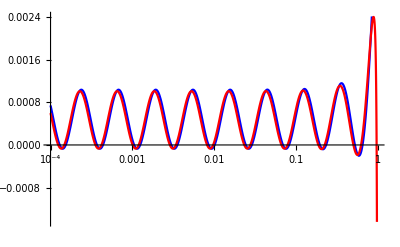

```mathematica
Block[{μ=3, k12=2, k34=1},LogLinearPlot[{2Re[Fexact], Fapprox},{s,10^-4,0.99},PlotStyle->{Blue, Red},GridLines->Automatic]]
```

```mathematica
Block[{μ=3,k12=2, k34=1},sValues=10^Range[Log10[10^-2],Log10[0.999],0.01];(*Logarithmic spacing*)
data=Table[{s^2/(k12 k34),2Re[Fexact],Fapprox},{s,sValues}];
Export["Desktop/SaddlePointNonLocal.csv",Prepend[data,{"s","Fexact","Fapprox"}]]]
(*Export data for python figure*)
```

Desktop/SaddlePointNonLocal.csv

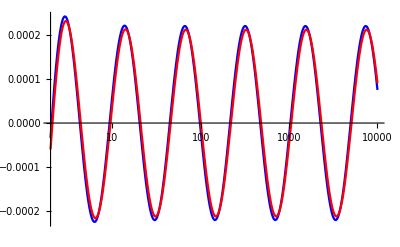

```mathematica
Block[{μ=4, k34=2, s=1},LogLinearPlot[{2Re[Fexact] ((k12 k34)/s^2)^(3/2), Fapprox ((k12 k34)/s^2)^(3/2) },{k12,2,10^4},PlotStyle->{Blue, Red},GridLines->Automatic]]
```

```mathematica
Block[{μ=4,k34=2, s=1},k12Values=10^Range[Log10[2],Log10[5 10^4],0.01];(*Logarithmic spacing*)
data=Table[{k12/k34,2Re[Fexact],Fapprox},{k12,k12Values}];
Export["Desktop/SaddlePointLocal.csv",Prepend[data,{"k12","Fexact","Fapprox"}]]]
(*Export data for python figure*)
```

Desktop/SaddlePointLocal.csv

#### Bootstrapping Helical Seed Correlators

```mathematica
<<MaTeX`;
texStyle={FontFamily->"Latin Modern Roman",FontSize->12};
```

#### From Bootstrap Equation

Full Exact Result

```mathematica
Clear[FBootBack, FBootSignal];
FBootBack[tu_,tv_]:=tu/2 (-1)^n/((n+1/2)^2+μ^2)(tu/tv)^n (1-tv)^n  HypergeometricPFQ[{1,1+n,1+n+I λ κ},{3/2+n-I μ,3/2+n+I μ},tu]HeavisideTheta[tv-tu]+tv/2 (-1)^n/((n+1/2)^2+μ^2)(tv/tu)^n (1-tu)^n  HypergeometricPFQ[{1,1+n,1+n+I λ κ},{3/2+n-I μ,3/2+n+I μ},tv]HeavisideTheta[tu-tv];
FBootSignal[tu_,tv_]:=(-1/(4 (-1+ⅇ^(4 π μ)) μ)I ⅇ^(-3 I π-2 λ π κ) (ⅇ^(2 λ π κ)+ⅇ^(2 π μ)) tu^(1/2-I μ) tv^(1/2+I μ) Gamma[1/2-I μ] Gamma[1/2+I μ] Hypergeometric2F1[1/2-I μ,1/2+I λ κ-I μ,1-2 I μ,tu] Hypergeometric2F1[1/2+I μ,1/2+I λ κ+I μ,1+2 I μ,tv]+1/(4 tu tv)I ⅇ^(1/2 I π (-6+2 I (λ κ+μ))) (tu tv)^(3/2-ⅈ μ) (Cosh[2 λ π κ]+Cosh[2 π μ]) Csch[2 π μ]^2 Gamma[1/2-I μ]^2 Gamma[1/2-I λ κ-I μ] Gamma[1/2+I λ κ-I μ] Hypergeometric2F1Regularized[1/2-I μ,1/2+I λ κ-I μ,1-2 I μ,tu] Hypergeometric2F1Regularized[1/2-I μ,1/2+I λ κ-I μ,1-2 I μ,tv]-1/4 I ⅇ^(-3 I π-2 λ π κ) (1+ⅇ^(2 π (λ κ+μ))) π tu^(1/2+I μ) tv^(1/2-I μ) Csch[2 π μ]^2 Gamma[1/2-I μ] Gamma[1/2+I μ] Hypergeometric2F1Regularized[1/2-I μ,1/2+I λ κ-I μ,1-2 I μ,tv] Hypergeometric2F1Regularized[1/2+I μ,1/2+I λ κ+I μ,1+2 I μ,tu]+1/(4 tu tv)ⅈ ⅇ^(1/2 π (-6 I-2 λ κ+2 μ)) (tu tv)^(3/2+I μ) (Cosh[2 λ π κ]+Cosh[2 π μ]) Csch[2 π μ]^2 Gamma[1/2+I μ]^2 Gamma[1/2-I λ κ+I μ] Gamma[1/2+I λ κ+I μ] Hypergeometric2F1Regularized[1/2+I μ,1/2+I λ κ+I μ,1+2 I μ,tu] Hypergeometric2F1Regularized[1/2+I μ,1/2+I λ κ+I μ,1+2 I μ,tv])HeavisideTheta[Re@tv-Re@tu]+(-1/(4 (-1+ⅇ^(4 π μ)) μ)ⅈ ⅇ^(-3 ⅈ π-2 π κ λ) (ⅇ^(2 π κ λ)+ⅇ^(2 π μ)) tu^(1/2+ⅈ μ) tv^(1/2-ⅈ μ) Gamma[1/2-ⅈ μ] Gamma[1/2+ⅈ μ] Hypergeometric2F1[1/2-ⅈ μ,1/2+ⅈ κ λ-ⅈ μ,1-2 ⅈ μ,tv] Hypergeometric2F1[1/2+ⅈ μ,1/2+ⅈ κ λ+ⅈ μ,1+2 ⅈ μ,tu]+1/(4 tu tv)ⅈ ⅇ^(1/2 ⅈ π (-6+2 ⅈ (κ λ+μ))) (tu tv)^(3/2-ⅈ μ) (Cosh[2 π κ λ]+Cosh[2 π μ]) Csch[2 π μ]^2 Gamma[1/2-ⅈ μ]^2 Gamma[1/2-ⅈ κ λ-ⅈ μ] Gamma[1/2+ⅈ κ λ-ⅈ μ] Hypergeometric2F1Regularized[1/2-ⅈ μ,1/2+ⅈ κ λ-ⅈ μ,1-2 ⅈ μ,tu] Hypergeometric2F1Regularized[1/2-ⅈ μ,1/2+ⅈ κ λ-ⅈ μ,1-2 ⅈ μ,tv]-1/4 ⅈ ⅇ^(-3 ⅈ π-2 π κ λ) (1+ⅇ^(2 π (κ λ+μ))) π tu^(1/2-ⅈ μ) tv^(1/2+ⅈ μ) Csch[2 π μ]^2 Gamma[1/2-ⅈ μ] Gamma[1/2+ⅈ μ] Hypergeometric2F1Regularized[1/2-ⅈ μ,1/2+ⅈ κ λ-ⅈ μ,1-2 ⅈ μ,tu] Hypergeometric2F1Regularized[1/2+ⅈ μ,1/2+ⅈ κ λ+ⅈ μ,1+2 ⅈ μ,tv]+1/(4 tu tv)ⅈ ⅇ^(1/2 π (-6 ⅈ-2 κ λ+2 μ)) (tu tv)^(3/2+ⅈ μ) (Cosh[2 π κ λ]+Cosh[2 π μ]) Csch[2 π μ]^2 Gamma[1/2+ⅈ μ]^2 Gamma[1/2-ⅈ κ λ+ⅈ μ] Gamma[1/2+ⅈ κ λ+ⅈ μ] Hypergeometric2F1Regularized[1/2+ⅈ μ,1/2+ⅈ κ λ+ⅈ μ,1+2 ⅈ μ,tu] Hypergeometric2F1Regularized[1/2+ⅈ μ,1/2+ⅈ κ λ+ⅈ μ,1+2 ⅈ μ,tv])HeavisideTheta[Re@tu-Re@tv];
(*The full solution is 2Re@FBootSignal+2Sum[Re@N@FBootBack, {n, 0, nn}]*)
```

Checking convergence inside the unit circle

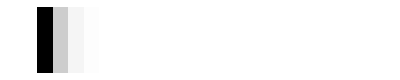

```mathematica
Block[{tu=1.2,tv=1.1,κ=0,μ=5,λ=1},
ArrayPlot[{Table[ 2Re@N@FBootBack[tu, tv],{n,0,20}]}]]
```

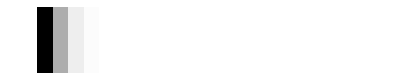

```mathematica
Block[{tu=1.2,tv=1.4,κ=0,μ=2,λ=1},
ArrayPlot[{Table[Re@(tu/2 (-1)^n/((n+1/2)^2+μ^2)(tu/tv)^n (1-tv)^n  HypergeometricPFQ[{1,1+n,1+n+I λ κ},{3/2+n-I μ,3/2+n+I μ},tu]),{n,0,20}]}]]
```

Execution time for nMax=2: 0.299128 seconds

Execution time for nMax=5: 0.355642 seconds

Execution time for nMax=10: 0.555539 seconds

Execution time for nMax=2: 1.35778 seconds

Execution time for nMax=5: 2.48974 seconds

Execution time for nMax=10: 4.95561 seconds

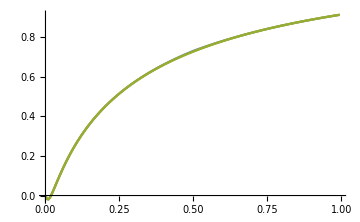
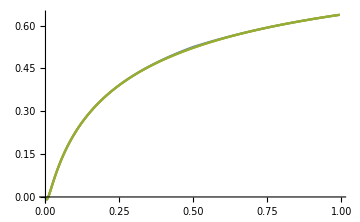

```mathematica
Block[{v=0.5, μ=1,λ=1, ϵ=10^-5},

(*Define a function to compute f-values for different n*)
computeF[nMax_]:=Module[{time,result},
{time,result}=AbsoluteTiming[ParallelTable[{u,2Re@FBootSignal[(2u)/(1+u), (2v)/(1+v)]+2 Sum[Re@N@FBootBack[(2u)/(1+u), (2v)/(1+v)],{n,0,nMax}]},{u,Range[0+ϵ,1-ϵ,5 10^-3]}]];
Print["Execution time for nMax=",nMax,": ",time," seconds"];
result]; 

(*Compute for kappa=0*)
Block[{κ=0},
f2Kappa0=computeF[2];
f5Kappa0=computeF[5];
f10Kappa0=computeF[10];
];

(*Compute for kappa=0.5*)
Block[{κ=0.5},
f2Kappa05=computeF[2];
f5Kappa05=computeF[5];
f10Kappa05=computeF[10];
];

plotKappa0=ListPlot[{f2Kappa0,f5Kappa0,f10Kappa0},Joined->True, ImageSize->Medium];
plotKappa05=ListPlot[{f2Kappa05,f5Kappa05,f10Kappa05},Joined->True, ImageSize->Medium];
{Show[plotKappa0],Show[plotKappa05]}
]
```

Checking convergence outside the unit circle

Execution time for nMax=2: 2.0464 seconds

Execution time for nMax=5: 3.9127 seconds

Execution time for nMax=10: 7.21694 seconds

Execution time for nMax=2: 2.97309 seconds

Execution time for nMax=5: 5.90846 seconds

Execution time for nMax=10: 11.002 seconds

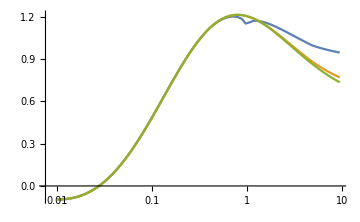
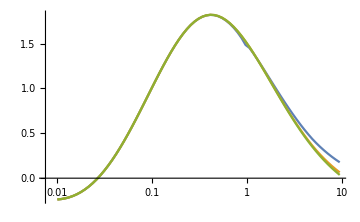

```mathematica
Block[{v=5, μ=1,λ=-1, ϵ=10^-5},

(*Define a function to compute f-values for different n*)
computeF[nMax_]:=Module[{time,result},
{time,result}=AbsoluteTiming[ParallelTable[{u,2 Re@FBootSignal[(2u)/(1+u), (2v)/(1+v)]+2 Sum[Re@N@FBootBack[(2u)/(1+u), (2v)/(1+v)],{n,0,nMax}]},{u,PowerRange[10^-2,10,1.1]}]];
Print["Execution time for nMax=",nMax,": ",time," seconds"];
result]; 

(*Compute for kappa=0*)
Block[{κ=0},
f2Kappa0=computeF[2];
f5Kappa0=computeF[5];
f10Kappa0=computeF[10];
];

(*Compute for kappa=0.5*)
Block[{κ=0.5},
f2Kappa05=computeF[2];
f5Kappa05=computeF[5];
f10Kappa05=computeF[10];
];

plotKappa0=ListLogLinearPlot[{f2Kappa0,f5Kappa0,f10Kappa0},Joined->True, ImageSize->Medium];
plotKappa05=ListLogLinearPlot[{f2Kappa05,f5Kappa05,f10Kappa05},Joined->True, ImageSize->Medium];
{Show[plotKappa0],Show[plotKappa05]}
]
```

Checking cosmological collider signal

Execution time for nMax=10: 0.590355 seconds

Execution time for nMax=10: 1.09602 seconds

Execution time for nMax=10: 1.10895 seconds

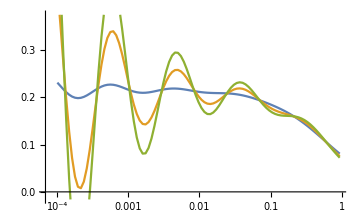

```mathematica
Block[{v=0.5, μ=3,λ=-1},

(*Define a function to compute f-values for different n*)
computeF[nMax_]:=Module[{time,result},
{time,result}=AbsoluteTiming[ParallelTable[{u,(2 Re@FBootSignal[(2u)/(1+u), (2v)/(1+v)]+2 Sum[Re@N@FBootBack[(2u)/(1+u), (2v)/(1+v)],{n,0,nMax}])/u},{u,PowerRange[10^-4,1,1.1]}]];
Print["Execution time for nMax=",nMax,": ",time," seconds"];
result]; 

(*Compute for different kappa*)
results={};
Do[
Block[{κ=ii},
fKappa=computeF[10];
AppendTo[results,{ii,fKappa}];
], {ii, {0, 1, 1.2}}];

ListLogLinearPlot[results[[All,2]],Joined->True, ImageSize->Medium]
]
```

```mathematica
Block[{v=0.5, μ=3,λ=-1},

(*Define a function to compute f-values for different kappa*)
computeF[uValues_]:=Module[{result},
result=ParallelTable[{u,2 Re@FBootSignal[(2u)/(1+u), (2v)/(1+v)],2 Sum[Re@N@FBootBack[(2u)/(1+u), (2v)/(1+v)],{n,0,10}]},{u,uValues}];
result]; 

umin=0.0001;
umax=0.9999;
nPoints=500;
uValues=Table[10^x,{x,Log10[umin],Log10[umax],(Log10[umax]-Log10[umin])/nPoints}];

Block[{κ=0},
f=computeF[uValues];
Export["/Users/deniswerth/Desktop/fBootmu3kappa0neglambda.csv",Prepend[f,{"u","Fsignal", "Fback"}]] ;
];

Block[{κ=0.5},
f=computeF[uValues];
Export["/Users/deniswerth/Desktop/fBootmu3kappa05neglambda.csv",Prepend[f,{"u","Fsignal", "Fback"}]] ;
];

Block[{κ=1},
f=computeF[uValues];
Export["/Users/deniswerth/Desktop/fBootmu3kappa1neglambda.csv",Prepend[f,{"u","Fsignal", "Fback"}]] ;
];

];
```

```mathematica
Block[{v=5, μ=3,λ=-1, κ=1},

(*Define a function to compute f-values for different kappa*)
computeF[nMax_, uValues_]:=Module[{result},
result=ParallelTable[{u,2 Re@FBootSignal[(2u)/(1+u), (2v)/(1+v)]+2 Sum[Re@N@FBootBack[(2u)/(1+u), (2v)/(1+v)],{n,0,nMax}]},{u,uValues}];
result]; 

umin=0.01;
umax=9.999;
nPoints=300;
uValues=Table[10^x,{x,Log10[umin],Log10[umax],(Log10[umax]-Log10[umin])/nPoints}];

f2=computeF[2, uValues];
Export["/Users/deniswerth/Desktop/fBootmu3kappa1nMax2.csv",Prepend[f2,{"u","F"}]] ;

f5=computeF[5, uValues];
Export["/Users/deniswerth/Desktop/fBootmu3kappa1nMax5.csv",Prepend[f5,{"u","F"}]] ;

f10=computeF[10, uValues];
Export["/Users/deniswerth/Desktop/fBootmu3kappa1nMax10.csv",Prepend[f10,{"u","F"}]] ;

f50=computeF[50, uValues];
Export["/Users/deniswerth/Desktop/fBootmu3kappa1nMax50.csv",Prepend[f50,{"u","F"}]] ;

];
```

#### From Spectral Representation

Full Exact Result

```mathematica
Clear[FSpectralRepSignal,FSpectralRepBack];
FSpectralRepSignal[u_,v_]:= 1/2 ⅈ π^2 (2 (-1+1/u^2)^((ⅈ λ κ)/2) (1/u)^(-1/2-ⅈ λ κ-ⅈ μ) ((1-u)/(1+u))^(-(ⅈ λ κ)/2) (-1+1/v^2)^((ⅈ λ κ)/2) (1/v)^(-1/2-ⅈ λ κ+ⅈ μ) ((1-v)/(1+v))^(-(ⅈ λ κ)/2) Csch[2 π μ] Hypergeometric2F1Regularized[1/4 (1+2 ⅈ λ κ-2 ⅈ μ),1/4 (3+2 ⅈ λ κ-2 ⅈ μ),1-ⅈ μ,v^2] Hypergeometric2F1Regularized[1/4 (1+2 ⅈ  λ κ+2 ⅈ μ),1/4 (3+2 ⅈ λ  κ+2 ⅈ μ),1+ⅈ μ,u^2]-1/Gamma[1/2+ⅈ  λ κ-ⅈ μ] 2^(1-2 ⅈ μ) (-1+1/u^2)^((ⅈ  λ κ)/2) (1/u)^(-1/2-ⅈ  λ κ-ⅈ μ) ((1-u)/(1+u))^(-(ⅈ λ  κ)/2) (-1+1/v^2)^((ⅈ  λ κ)/2) (1/v)^(-1/2-ⅈ  λ κ-ⅈ μ) ((1-v)/(1+v))^(-(ⅈ  λ κ)/2) Csch[2 π μ] Gamma[1/2+ⅈ  λ κ+ⅈ μ] Hypergeometric2F1Regularized[1/4 (1+2 ⅈ  λ κ+2 ⅈ μ),1/4 (3+2 ⅈ  λ κ+2 ⅈ μ),1+ⅈ μ,u^2] Hypergeometric2F1Regularized[1/4 (1+2 ⅈ λ  κ+2 ⅈ μ),1/4 (3+2 ⅈ  λ κ+2 ⅈ μ),1+ⅈ μ,v^2]+1/Gamma[1/2-ⅈ κ λ+ⅈ μ] ⅇ^(-π ( λ κ+μ)) Gamma[1/2+ⅈ κ λ+ⅈ μ] Hypergeometric2F1Regularized[1/2-ⅈ μ,1/2+ⅈ μ,1+ⅈ  λ κ,(-1+u)/(2 u)] Hypergeometric2F1Regularized[1/2-ⅈ μ,1/2+ⅈ μ,1+ⅈ  λ κ,(-1+v)/(2 v)] Sech[π μ]^2)HeavisideTheta[v-u]+1/2 ⅈ π^2 (2 (-1+1/u^2)^((ⅈ  λ κ)/2) (1/u)^(-1/2-ⅈ  λ κ+ⅈ μ) ((1-u)/(1+u))^(-(ⅈ  λ κ)/2) (-1+1/v^2)^((ⅈ  λ κ)/2) (1/v)^(-1/2-ⅈ  λ κ-ⅈ μ) ((1-v)/(1+v))^(-(ⅈ  λ κ)/2) Csch[2 π μ] Hypergeometric2F1Regularized[1/4 (1+2 ⅈ λ  κ-2 ⅈ μ),1/4 (3+2 ⅈ λ  κ-2 ⅈ μ),1-ⅈ μ,u^2] Hypergeometric2F1Regularized[1/4 (1+2 ⅈ  λ κ+2 ⅈ μ),1/4 (3+2 ⅈ  λ κ+2 ⅈ μ),1+ⅈ μ,v^2]-1/Gamma[1/2+ⅈ  λ κ-ⅈ μ] 2^(1-2 ⅈ μ) (-1+1/u^2)^((ⅈ λ  κ)/2) (1/u)^(-1/2-ⅈ  λ κ-ⅈ μ) ((1-u)/(1+u))^(-(ⅈ  λ κ)/2) (-1+1/v^2)^((ⅈ  λ κ)/2) (1/v)^(-1/2-ⅈ  λ κ-ⅈ μ) ((1-v)/(1+v))^(-(ⅈ  λ κ)/2) Csch[2 π μ] Gamma[1/2+ⅈ λ  κ+ⅈ μ] Hypergeometric2F1Regularized[1/4 (1+2 ⅈ  λ κ+2 ⅈ μ),1/4 (3+2 ⅈ λ  κ+2 ⅈ μ),1+ⅈ μ,u^2] Hypergeometric2F1Regularized[1/4 (1+2 ⅈ  λ κ+2 ⅈ μ),1/4 (3+2 ⅈ  λ κ+2 ⅈ μ),1+ⅈ μ,v^2]+1/Gamma[1/2-ⅈ κ λ+ⅈ μ] ⅇ^(-π ( λ κ+μ)) Gamma[1/2+ⅈ κ λ+ⅈ μ] Hypergeometric2F1Regularized[1/2-ⅈ μ,1/2+ⅈ μ,1+ⅈ  λ κ,(-1+u)/(2 u)] )HeavisideTheta[u-v];
FSpectralRepBack[u_,v_]:= (-π((u+1)(v+1))^(I λ κ)(1+2n)/((n+1/2)^2+μ^2)(v/2)^(n+1)(u/2)^(n+1)Gamma[1+n+I λ κ]/Gamma[-n+I λ κ] Hypergeometric2F1Regularized[(1+n)/2+(I λ κ)/2, 1+n/2+(I λ κ)/2, 3/2+n, u^2]Hypergeometric2F1Regularized[(1+n)/2+(I λ κ)/2, 1+n/2+(I λ κ)/2, 3/2+n, v^2]+u((u+1)(v+1))^(I λ κ)(-1)^n/((n+1/2)^2+μ^2)(u/v)^n Hypergeometric2F1[(1+n)/2+(I λ κ)/2, 1+n/2+(I λ κ)/2, 3/2+n, u^2]Hypergeometric2F1[(1-n)/2+(I λ κ)/2, -n/2+(I λ κ)/2, 1/2-n, v^2])HeavisideTheta[v-u]+(-π((v+1)(u+1))^(I λ κ)(1+2n)/((n+1/2)^2+μ^2)(u/2)^(n+1)(v/2)^(n+1)Gamma[1+n+I λ κ]/Gamma[-n+I λ κ] Hypergeometric2F1Regularized[(1+n)/2+(I λ κ)/2, 1+n/2+(I λ κ)/2, 3/2+n, v^2]Hypergeometric2F1Regularized[(1+n)/2+(I λ κ)/2, 1+n/2+(I λ κ)/2, 3/2+n, u^2]+v((v+1)(u+1))^(I λ κ)(-1)^n/((n+1/2)^2+μ^2)(v/u)^n Hypergeometric2F1[(1+n)/2+(I λ κ)/2, 1+n/2+(I λ κ)/2, 3/2+n, v^2]Hypergeometric2F1[(1-n)/2+(I λ κ)/2, -n/2+(I λ κ)/2, 1/2-n, u^2])HeavisideTheta[u-v];
(*The full solution is 2Re@FSpectralRepSignal+2Sum[Re@N@FSpectralRepBack, {n, 0, nn}]*)
```

Checking convergence inside the unit circle

Execution time for nMax=2: 0.304678 seconds

Execution time for nMax=5: 0.410938 seconds

Execution time for nMax=10: 0.699324 seconds

Execution time for nMax=2: 0.114942 seconds

Execution time for nMax=5: 0.226505 seconds

Execution time for nMax=10: 0.546577 seconds

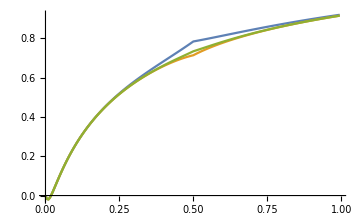
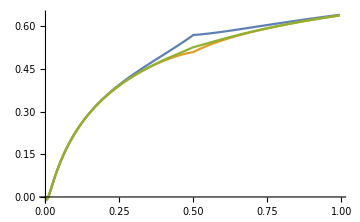

```mathematica
Block[{v=0.5, μ=1,λ=1, ϵ=10^-5},

(*Define a function to compute f-values for different n*)
computeF[nMax_]:=Module[{time,result},
{time,result}=AbsoluteTiming[ParallelTable[{u,2Re@FSpectralRepSignal[u, v]+ 2Sum[Re@N@FSpectralRepBack[u, v],{n,0,nMax}]},{u,Range[0+ϵ,1-ϵ,5 10^-3]}]];
Print["Execution time for nMax=",nMax,": ",time," seconds"];
result]; 

(*Compute for kappa=0*)
Block[{κ=0},
f2Kappa0=computeF[2];
f5Kappa0=computeF[5];
f10Kappa0=computeF[10];
];

(*Compute for kappa=0.5*)
Block[{κ=0.5},
f2Kappa05=computeF[2];
f5Kappa05=computeF[5];
f10Kappa05=computeF[10];
];

plotKappa0=ListPlot[{f2Kappa0,f5Kappa0,f10Kappa0},Joined->True, ImageSize->Medium];
plotKappa05=ListPlot[{f2Kappa05,f5Kappa05,f10Kappa05},Joined->True, ImageSize->Medium];
{Show[plotKappa0],Show[plotKappa05]}
]
```

```mathematica
Block[{u=1.2, v=5,κ=0.5,μ=1 ,λ=-1, nMax=30},
{ParallelSum[N@FSpectralRepBack[u,v],{n,0,nMax}],ParallelSum[N@FBootBack[(2u)/(1+u),(2v)/(1+v)],{n,0,nMax}]}//Print;
]
```

{0.510768-0.60874 ⅈ,0.510823-0.609986 ⅈ}

```mathematica
Block[{u=1.2, v=5,κ=0.5,μ=1 ,λ=-1},
{N@FSpectralRepSignal[u,v],N@FBootSignal[(2u)/(1+u),(2v)/(1+v)]}//Print;
]
```

{0.177552+2.22921 ⅈ,0.177552+2.22921 ⅈ}

Checking convergence outside the unit circle

Execution time for nMax=2: 0.130825 seconds

Execution time for nMax=5: 0.159824 seconds

Execution time for nMax=10: 0.264706 seconds

Execution time for nMax=50: 1.24712 seconds

Execution time for nMax=2: 0.067955 seconds

Execution time for nMax=5: 0.088556 seconds

Execution time for nMax=10: 0.159025 seconds

Execution time for nMax=50: 1.67795 seconds

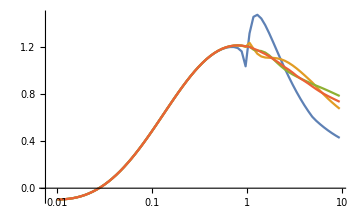
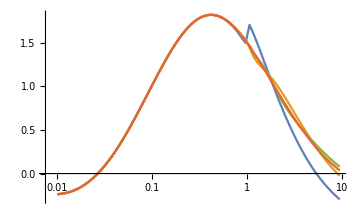

```mathematica
Block[{v=5, μ=1,λ=-1},

(*Define a function to compute f-values for different n*)
computeF[nMax_]:=Module[{time,result},
{time,result}=AbsoluteTiming[ParallelTable[{u,2 Re@FSpectralRepSignal[u, v]+2 Sum[Re@N@FSpectralRepBack[u, v],{n,0,nMax}]},{u,PowerRange[10^-2,10,1.1]}]];
Print["Execution time for nMax=",nMax,": ",time," seconds"];
result]; 

(*Compute for kappa=0*)
Block[{κ=0},
f2Kappa0=computeF[2];
f5Kappa0=computeF[5];
f10Kappa0=computeF[10];
f50Kappa0=computeF[50];
];

(*Compute for kappa=0.5*)
Block[{κ=0.5},
f2Kappa05=computeF[2];
f5Kappa05=computeF[5];
f10Kappa05=computeF[10];
f50Kappa05=computeF[50];
];

plotKappa0=ListLogLinearPlot[{f2Kappa0,f5Kappa0,f10Kappa0, f50Kappa0},Joined->True, ImageSize->Medium];
plotKappa05=ListLogLinearPlot[{f2Kappa05,f5Kappa05,f10Kappa05, f50Kappa05},Joined->True, ImageSize->Medium];
{Show[plotKappa0],Show[plotKappa05]}
]
```

Checking cosmological collider signal

Execution time for nMax=10: 0.088757 seconds

Execution time for nMax=10: 0.16978 seconds

Execution time for nMax=10: 0.157853 seconds

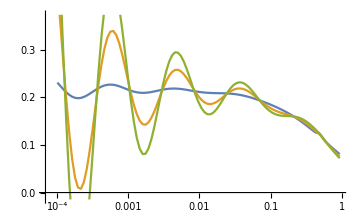

```mathematica
Block[{v=0.5, μ=3,λ=-1},

(*Define a function to compute f-values for different n*)
computeF[nMax_]:=Module[{time,result},
{time,result}=AbsoluteTiming[ParallelTable[{u,(2 Re@FSpectralRepSignal[u, v]+2 Sum[Re@N@FSpectralRepBack[u, v],{n,0,nMax}])/u},{u,PowerRange[10^-4,1,1.1]}]];
Print["Execution time for nMax=",nMax,": ",time," seconds"];
result]; 

(*Compute for different kappa*)
results={};
Do[
Block[{κ=ii},
fKappa=computeF[10];
AppendTo[results,{ii,fKappa}];
], {ii, {0, 1, 1.2}}];

ListLogLinearPlot[results[[All,2]],Joined->True, ImageSize->Medium]
]
```

```mathematica
Block[{v=5, μ=3,λ=-1, κ=1},

(*Define a function to compute f-values for different kappa*)
computeF[nMax_, uValues_]:=Module[{result},
result=ParallelTable[{u,2 Re@FSpectralRepSignal[u, v]+2 Sum[Re@N@FSpectralRepBack[u, v],{n,0,nMax}]},{u,uValues}];
result]; 

umin=0.01;
umax=9.999;
nPoints=300;
uValues=Table[10^x,{x,Log10[umin],Log10[umax],(Log10[umax]-Log10[umin])/nPoints}];

f2=computeF[2, uValues];
Export["/Users/deniswerth/Desktop/fSpectralRepmu3kappa1nMax2.csv",Prepend[f2,{"u","F"}]] ;

f5=computeF[5, uValues];
Export["/Users/deniswerth/Desktop/fSpectralRepmu3kappa1nMax5.csv",Prepend[f5,{"u","F"}]] ;

f10=computeF[10, uValues];
Export["/Users/deniswerth/Desktop/fSpectralRepmu3kappa1nMax10.csv",Prepend[f10,{"u","F"}]] ;

f50=computeF[50, uValues];
Export["/Users/deniswerth/Desktop/fSpectralRepmu3kappa1nMax50.csv",Prepend[f50,{"u","F"}]] ;

];
```

Comparing convergence

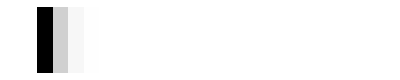
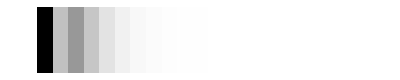

```mathematica
Block[{u=0.4,v=0.6,κ=2,μ=5,λ=-1, nMax=20},
Boot=ArrayPlot[{Table[ Re@N@FBootBack[(2u)/(1+u), (2v)/(1+v)],{n,0,nMax}]}];
SpectralRep=ArrayPlot[{Table[ Re@N@FSpectralRepBack[u, v],{n,0,nMax}]}];
{Show[Boot], Show[SpectralRep]}
]
```

```mathematica
Block[{u=2,v=5,μ=1,κ=0.5,λ=-1, nMaxMax=50},
nMaxValues = Table[nMax, {nMax, 0, nMaxMax}];

BootTime=Table[{nMax, Timing[Re@N@FBootSignal[(2u)/(1+u), (2v)/(1+v)]+ParallelSum[Re@N@FBootBack[(2u)/(1+u), (2v)/(1+v)], {n, 0, nMax}]][[1]]}, {nMax, nMaxValues}];
Export["/Users/deniswerth/Desktop/BootTimingmu1kappa05outside.csv",Prepend[BootTime,{"nMax","time"}]] ;

SpectralRepTime=Table[{nMax, Timing[Re@N@FSpectralRepSignal[u, v]+ParallelSum[Re@N@FSpectralRepBack[u, v], {n, 0, nMax}]][[1]]}, {nMax, nMaxValues}];
Export["/Users/deniswerth/Desktop/SpectralRepTimingmu1kappa05outside.csv",Prepend[SpectralRepTime,{"nMax","time"}]] ;

];
```

Picking poles

```mathematica
IntegrandF0 = (2 Exp[2 π λ κ])/π 1/(2π)(Gamma[1/2+I μ]Gamma[1/2-I μ]Gamma[1+I μ]Gamma[1-I μ])/(Gamma[1/2+I μ+I λ κ] Gamma[1/2-I μ+I λ κ])(LegendreQ[-I μ-1/2, I λ κ, 3, 1/u]LegendreQ[-I μ-1/2, I λ κ, 3, 1/v])/(μ^2+ν^2);
IntegrandFpm = -(2 Exp[2 π λ κ])/π 1/(2π)(Gamma[1/2+I μ]Gamma[1/2-I μ]Gamma[1+I μ]Gamma[1-I μ])/(Gamma[1/2+I μ+I λ κ] Gamma[1/2-I μ+I λ κ])(LegendreQ[-I μ-1/2, I λ κ, 3, 1/u]LegendreQ[+I μ-1/2, I λ κ, 3, 1/v])/(μ^2+ν^2);
```

```mathematica
Block[{ν=1.2, λ=+1, κ=1, u=0.2, v=0.4,a=2, n=1},
ComplexPlot[
IntegrandF0(μ^2+ν^2), {μ, -a(1+I), +a(1+I)},
Epilog->{Black, PointSize[Large],Point[{0,(1/2+n)}]}
]
]
```

-Graphics-

```mathematica
Sum[2I π Residue[IntegrandF0 , {μ, I n}] + 2I π Residue[IntegrandFpm, {μ, I n}], {n, 0, 3}]//FullSimplify
```

0

```mathematica
Block[{μ=2.5, λ=+1, κ=1.2, z=1/0.4},
LegendreQ[-I μ-1/2,I λ κ,3,z]//Print;
Exp[-π λ κ] √(π/2)Gamma[1/2-I μ+I λ κ](z^2-1)^(I λ κ/2)2^(I μ)z^(-1/2+I μ-I λ κ)Hypergeometric2F1Regularized[(3/2-I μ+I λ κ)/2,(1/2-I μ+I λ κ)/2,1-I μ,1/z^2]//Print;
]
```

0.0473805-0.0627821 ⅈ

0.0473805-0.0627821 ⅈ

```mathematica
IntegrandF0/.LegendreQ[a_,b_,3,z_]:>ⅇ^(ⅈ π b)√(π/2)Gamma[1+a+b](z^2-1)^(b/2)2^(-a-1/2)z^(-a-1-b)Hypergeometric2F1Regularized[(3/2+a+1/2+b)/2,(1/2+a+1/2+b)/2,a+3/2,1/z^2]//Simplify
```

(2^(-1+2 ⅈ μ) (-1+1/u^2)^((ⅈ κ λ)/2) (1/u)^(-1/2-ⅈ κ λ+ⅈ μ) (-1+1/v^2)^((ⅈ κ λ)/2) (1/v)^(-1/2-ⅈ κ λ+ⅈ μ) Gamma[1/2+ⅈ κ λ-ⅈ μ] Gamma[1-2 ⅈ μ] Gamma[1+2 ⅈ μ] Hypergeometric2F1Regularized[1/4 ⅈ (-ⅈ+2 κ λ-2 μ),1/4 ⅈ (-3 ⅈ+2 κ λ-2 μ),1-ⅈ μ,u^2] Hypergeometric2F1Regularized[1/4 ⅈ (-ⅈ+2 κ λ-2 μ),1/4 ⅈ (-3 ⅈ+2 κ λ-2 μ),1-ⅈ μ,v^2])/((μ^2+ν^2) Gamma[1/2+ⅈ κ λ+ⅈ μ])

```mathematica
Clear[FDeltaG, FG0, FGpm];
Fpm =  π^2 Exp[-π λ κ]/(2 Cosh[π μ]^2)Hypergeometric2F1Regularized[1/2-I μ, 1/2+I μ, 1+I λ κ, 1/2-1/(2u)]Hypergeometric2F1Regularized[1/2-I μ, 1/2+I μ, 1-I λ κ, 1/2-1/(2v)];
FDeltaG = I π^2 Exp[-π(μ+λ κ)]/(2 Cosh[π μ]^2)Gamma[1/2+I μ+I λ κ]/Gamma[1/2+I μ-I λ κ] Hypergeometric2F1Regularized[1/2-I μ, 1/2+I μ, 1+I λ κ, 1/2-1/(2u)]Hypergeometric2F1Regularized[1/2-I μ, 1/2+I μ, 1+I λ κ, 1/2-1/(2v)];
FG0 = (((1-u)/(1+u))((1-v)/(1+v)))^(-I λ κ)(2I π Residue[IntegrandF0 , {μ, I ν}]) /.{ν->I μ}//Simplify;
FGpm = (((1-u)/(1+u))((1-v)/(1+v)))^(-I λ κ)(2I π Residue[IntegrandFpm, {μ, I ν}]) /.{ν->I μ}//Simplify;
test = -π^2 Exp[-π λ κ]/(2 Cosh[π μ]^2)Hypergeometric2F1Regularized[1/2-I μ, 1/2+I μ, 1-I λ κ, 1/2+1/(2u)]Hypergeometric2F1Regularized[1/2-I μ, 1/2+I μ, 1+I λ κ, 1/2-1/(2v)];
```

```mathematica
Block[{u=0.2, v=0.4, μ=1, λ=+1, κ=0},
FDeltaG+FG0+FGpm//Print;
FSpectralRepSignal[u, v]//Print;
]
```

0.0630077+0.0126276 ⅈ

0.0630077+0.0126276 ⅈ